```mathematica
Get[NotebookDirectory[]<>"MagnusFuncs.m"]
```

You are using the version of NCAlgebra which is found in:

/Users/jesse/NC/

You can now use "<< NCAlgebra`" to load NCAlgebra.

------------------------------------------------------------
NCAlgebra - Version 5.0.3
Compatible with Mathematica Version 10 and above

Authors:

  J. William Helton*
  Mauricio de Oliveira&

* Math, UCSD, La Jolla, CA
& MAE, UCSD, La Jolla, CA

with major earlier contributions by:

  Mark Stankus$ 
  Robert L. Miller#

$ Math, Cal Poly San Luis Obispo
# General Atomics Corp

Copyright: 
  Helton and de Oliveira 2017
  Helton 2002
  Helton and Miller June 1991
  All rights reserved.

The program was written by the authors and by:
  David Hurst, Daniel Lamm, Orlando Merino, Robert Obar,
  Henry Pfister, Mike Walker, John Wavrik, Lois Yu,
  J. Camino, J. Griffin, J. Ovall, T. Shaheen, John Shopple. 
  The beginnings of the program come from eran@slac.
  Considerable recent help came from Igor Klep.

Current primary support is from the 
  NSF Division of Mathematical Sciences.
  
This program was written with support from 
  AFOSR, NSF, ONR, Lab for Math and Statistics at UCSD,
  UCSD Faculty Mentor Program,
  and US Department of Education.

For NCAlgebra updates see:

  www.github.com/NCAlgebra/NC
  www.math.ucsd.edu/~ncalg

------------------------------------------------------------

## Original Hamiltonian ME

```mathematica
Horig=H1/4*(Cos[phi]*sx+Cos[2*ww*t+phi]sx+Sin[phi]sy-Sin[2*ww*t+phi]*sy)+Delta/2*sz
```

(Delta sz)/2+1/4 H1 (sx Cos[phi]+sx Cos[phi+2 t ww]+sy Sin[phi]-sy Sin[phi+2 t ww])

```mathematica
taylorReplacements={H1->E0+E1 (t-ts),H1D->E1}
```

{H1→E0+E1 (t-ts),H1D→E1}

```mathematica
Hsimple=Horig/.{phi->0,Delta->0}/.taylorReplacements//FS
```

1/4 (E0+E1 (t-ts)) (sx+sx Cos[2 t ww]-sy Sin[2 t ww])

```mathematica
Remove[Ωsimple];
```

```mathematica
max=2;
SetNonCommutative[h];
MIsimple=JesseGetMagnusIntegrands[h,Ωsimple,max]/.h->Hsimple
```

{-1/4 ⅈ (E0+E1 (t-ts)) (sx+sx Cos[2 t ww]-sy Sin[2 t ww]),1/8 ⅈ (E0+E1 (t-ts)) (Commutator[Ωsimple_1[t,t0],sx]+Commutator[Ωsimple_1[t,t0],sx] Cos[2 t ww]-Commutator[Ωsimple_1[t,t0],sy] Sin[2 t ww])}

```mathematica
Do[
Subscript[Ωsimple, i][t_,t0_]=JesseDoMagnusIntegration[MIsimple[[i]], max];
Print[Subscript[Ωsimple, i][tb,ta]];
,{i,max}
];
```

** Begin integrating the next Magnus integrand, at date and time {2018,1,18,15,16}

SigmaComRules Done:  {15,16}

> picking and simplifying done:  {15,16}  trimmed coeffs:  0

> assembling and simplifying done: {15,16}

Trimming Done:  {15,16}

Starting termwise integration on 6 terms

Term: 1

Term: 2

Term: 3

Term: 4

Term: 5

Term: 6

Integration from `t0' to `t' done:  {15,16}

> picking and simplifying done:  {15,16}  trimmed coeffs:  0

> assembling and simplifying done: {15,16}

Post-integration trim done:  {15,16}

-1/8 ⅈ (-E1 sx ta^2+E1 sx tb^2-2 sx ta (E0-E1 ts)+2 sx tb (E0-E1 ts)-(E1 ta (sy Cos[2 ta ww]+sx Sin[2 ta ww]))/ww+(E1 tb (sy Cos[2 tb ww]+sx Sin[2 tb ww]))/ww-(E1 Sin[(-ta+tb) ww] (sy Cos[(ta+tb) ww]+sx Sin[(ta+tb) ww]))/ww^2+(2 (E0-E1 ts) Sin[(-ta+tb) ww] (sx Cos[(ta+tb) ww]-sy Sin[(ta+tb) ww]))/ww)

** Begin integrating the next Magnus integrand, at date and time {2018,1,18,15,16}

SigmaComRules Done:  {15,16}

> picking and simplifying done:  {15,16}  trimmed coeffs:  4

> assembling and simplifying done: {15,16}

Trimming Done:  {15,16}

Starting termwise integration on 27 terms

Term: 1

Term: 2

Term: 3

Term: 4

Term: 5

Term: 6

Term: 7

Term: 8

Term: 9

Term: 10

Term: 11

Term: 12

Term: 13

Term: 14

Term: 15

Term: 16

Term: 17

Term: 18

Term: 19

Term: 20

Term: 21

Term: 22

Term: 23

Term: 24

Term: 25

Term: 26

Term: 27

Integration from `t0' to `t' done:  {15,17}

> picking and simplifying done:  {15,17}  trimmed coeffs:  5

> assembling and simplifying done: {15,17}

Post-integration trim done:  {15,17}

1/(32 ww^2)ⅈ sz (E0-E1 ts)^2 (ta ww-tb ww+(-ta+tb) ww Cos[2 ta ww]+(-ta+tb) ww Cos[2 tb ww]-Cos[(ta-2 tb) ww] Sin[ta ww]+Sin[2 ta ww]-1/2 Sin[2 tb ww])

```mathematica
Subscript[Ωsimple, 1][tb,ta]
```

-1/8 ⅈ (-E1 sx ta^2+E1 sx tb^2-2 sx ta (E0-E1 ts)+2 sx tb (E0-E1 ts)-(E1 ta (sy Cos[2 ta ww]+sx Sin[2 ta ww]))/ww+(E1 tb (sy Cos[2 tb ww]+sx Sin[2 tb ww]))/ww-(E1 Sin[(-ta+tb) ww] (sy Cos[(ta+tb) ww]+sx Sin[(ta+tb) ww]))/ww^2+(2 (E0-E1 ts) Sin[(-ta+tb) ww] (sx Cos[(ta+tb) ww]-sy Sin[(ta+tb) ww]))/ww)

```mathematica
I/tc*Subscript[Ωsimple, 1][ta+tc,ta]//FS//CWW
```

1/4 sx (E0+E1 ta-E1 ts)+(E1 π sx+E1 sy Cos[2 ta ww]+E1 sx Sin[2 ta ww])/(8 ww)

```mathematica
I/tc*Subscript[Ωsimple, 2][ta+tc,ta]//FS//CWW
```

-(sz (E0-E1 ts)^2 (-1+2 Cos[2 ta ww]))/(32 ww)

## Calculate effective Hamiltonian

```mathematica
h0=Coefficient[HmeS12,1/ww,0]//FS
```

1/4 sx (E0-E1 ts)

```mathematica
h0enveloped=h0
```

1/4 sx (E0+E1 (ta-ts))

```mathematica
Remove[Ωh0];
max=2;
SetNonCommutative[h];
MIh0=JesseGetMagnusIntegrands[h,Ωh0,max]/.h->h0enveloped

Do[
Subscript[Ωh0, i][t_,t0_]=JesseDoMagnusIntegration[MIh0[[i]], max,False];
Print[Subscript[Ωh0, i][tb,ta]];
,{i,max}
];
```

{-1/4 ⅈ sx (E0+E1 (t-ts)+E1 (ta-ts)),1/8 ⅈ (E0+E1 (t-ts)+E1 (ta-ts)) Commutator[Ωh0_1[t,t0],sx]}

** Begin integrating the next Magnus integrand, at date and time {2018,1,18,14,41}

SigmaComRules Done:  {14,41}

Skipping trim

Starting termwise integration on 4 terms

Term: 1

Term: 2

Term: 3

Term: 4

Integration from `t0' to `t' done:  {14,41}

Skipping trim, simplifying instead

Simplifying done:  {14,41}

-1/8 ⅈ sx (-ta+tb) (2 E0+E1 (3 ta+tb-4 ts))

** Begin integrating the next Magnus integrand, at date and time {2018,1,18,14,41}

SigmaComRules Done:  {14,41}

Skipping trim

Starting termwise integration on 0 terms

Integration from `t0' to `t' done:  {14,41}

Skipping trim, simplifying instead

Simplifying done:  {14,41}

0

```mathematica
h0ME=I/tc*Subscript[Ωh0, 1][ta+tc,ta]
```

1/8 sx (2 E0+E1 (4 ta-4 ts+π/ww))

```mathematica
h1=Coefficient[HS12,1/ww,1]-Coefficient[h0ME,1/ww,1]//FS
```

1/384 (-48 E1 π sx-12 sz (E0+E1 (ta-ts))^2 (-1+2 Cos[2 ta ww])+48 E1 (sy Cos[2 ta ww]+sx (π+Sin[2 ta ww])))

## Effective Hamiltonian ME

```mathematica
Heff=1/4 sx H1+(H1D sy Cos[2 α0]+H1D sx Sin[2α0])/(8 ww)/.taylorReplacements//FS
```

(2 sx (E0+E1 t) ww+E1 sy Cos[2 α0]+E1 sx Sin[2 α0])/(8 ww)

```mathematica
Remove[Ωeff]
```

```mathematica
max=5;
SetNonCommutative[h];
MIeff=JesseGetMagnusIntegrands[h,Ωeff,max]/.h->Heff;
```

$Aborted

```mathematica
Do[
Subscript[Ωeff, i][t_,t0_]=JesseDoMagnusIntegration[MIeff[[i]], max];
(*Print[Subscript[WWeff, i][t,t0]];*)
,{i,max}
];
```

* Begin integrating the next Magnus integrand, at date and time {2017,12,8,15,48}

SigmaComRules Done:  {15,48}

> picking and simplifying done:  {15,48}  trimmed coeffs:  0

> assembling and FULL simplifying done: {15,48}

Trimming Done:  {15,48}

Integration from `t0' to `t' done:  {15,48}

> picking and simplifying done:  {15,48}  trimmed coeffs:  0

> assembling and FULL simplifying done: {15,48}

Post-integration trim done:  {15,48}

* Begin integrating the next Magnus integrand, at date and time {2017,12,8,15,48}

SigmaComRules Done:  {15,48}

> picking and simplifying done:  {15,48}  trimmed coeffs:  0

> assembling and FULL simplifying done: {15,48}

Trimming Done:  {15,48}

Integration from `t0' to `t' done:  {15,48}

> picking and simplifying done:  {15,48}  trimmed coeffs:  0

> assembling and FULL simplifying done: {15,48}

Post-integration trim done:  {15,48}

* Begin integrating the next Magnus integrand, at date and time {2017,12,8,15,48}

SigmaComRules Done:  {15,48}

> picking and simplifying done:  {15,48}  trimmed coeffs:  0

> assembling and FULL simplifying done: {15,48}

Trimming Done:  {15,48}

Integration from `t0' to `t' done:  {15,48}

> picking and simplifying done:  {15,48}  trimmed coeffs:  0

> assembling and FULL simplifying done: {15,48}

Post-integration trim done:  {15,48}

* Begin integrating the next Magnus integrand, at date and time {2017,12,8,15,48}

SigmaComRules Done:  {15,48}

> picking and simplifying done:  {15,48}  trimmed coeffs:  24

> assembling and FULL simplifying done: {15,48}

Trimming Done:  {15,48}

Integration from `t0' to `t' done:  {15,48}

> picking and simplifying done:  {15,48}  trimmed coeffs:  0

> assembling and FULL simplifying done: {15,48}

Post-integration trim done:  {15,48}

* Begin integrating the next Magnus integrand, at date and time {2017,12,8,15,48}

SigmaComRules Done:  {15,48}

```mathematica
I/tc Subscript[Ωeff, 1][ta+tc,ta]//FS//CWW
```

1/4 sx (Hd0+Hd1 ta)+(Hd1 π sx+Hd1 sy Cos[2 α0]+Hd1 sx Sin[2 α0])/(8 ww)

```mathematica
I/tc Subscript[Ωeff, 2][ta+tc,ta]
```

(Hd1^2 π^2 sz Cos[2 α0])/(192 ww^3)

```mathematica
I/tc Subscript[Ωeff, 3][ta+tc,ta]
```

-(Hd1^3 π^4 sy Cos[2 α0])/(7680 ww^5)

```mathematica
I/tc Subscript[Ωeff, 4][ta+tc,ta]
```

(Hd0^2 Hd1^2 π^4 sz Cos[2 α0])/(46080 ww^5)

## First order counter-wave averaging

```mathematica
counterWaveLinDrive[t_]:={t*Cos[2*t],-t*Sin[2*t]};
counterWaveConstDrive[t_]:={Cos[2*t],Sin[2*t]};
```

```mathematica
avgPointLinDrive=Integrate[counterWaveLinDrive[t],{t,0,Pi}]
avgPointConstDrive=Integrate[counterWaveConstDrive[t],{t,0,Pi}]
```

{0,π/2}

{0,0}

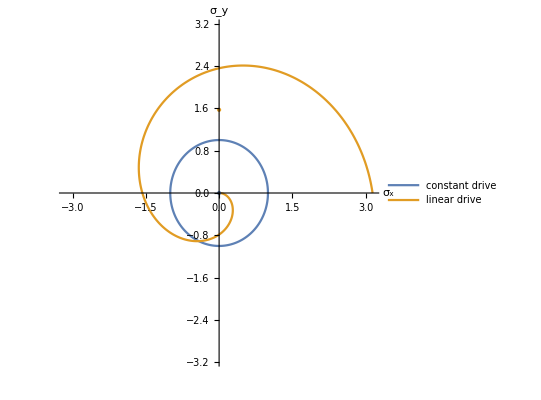

```mathematica
Show[{
ParametricPlot[{counterWaveConstDrive[t],counterWaveLinDrive[t]},{t,0,Pi},AspectRatio->1,PlotRange->{{-Pi, Pi},{-Pi,Pi}},AxesLabel->{"σ_x","σ_y"},PlotLegends->Placed[{"constant drive","linear drive"},{0.8,0.3}]],
Graphics[{PointSize[Large],ColorData[97,"ColorList"][[1]],Point[avgPointConstDrive],ColorData[97,"ColorList"][[2]],Point[avgPointLinDrive]}]
}]
```

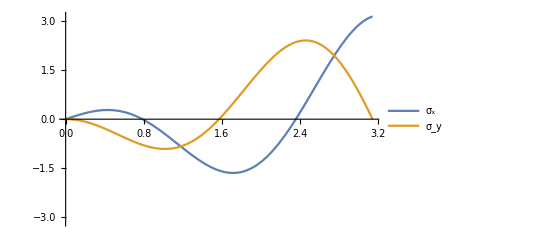

```mathematica
Plot[Evaluate[counterWaveLinDrive[t]],{t,0,Pi},PlotLegends->{"σ_x","σ_y"},PlotRange->{-Pi,Pi}]
```

```mathematica
simpleHf[t_]:=env[t]/4*(sx+sx Cos[2 t ww]-sy Sin[2 t ww])
```

```mathematica
o2int=1/2  Commutator[-I h[t1],-I h[t2]]
```

-1/2 Commutator[h[t1],h[t2]]

```mathematica
o2intHreal=Collect[o2int/.h->simpleHf//.SigmaComRules//Expand,env[t1]env[t2]sz]//FS
```

-1/4 ⅈ sz Cos[t1 ww] Cos[t2 ww] env[t1] env[t2] Sin[(t1-t2) ww]

```mathematica
separableitgd=o2intHreal/.Sin[arg_]:>TrigExpand[Sin[Expand[arg]]]//Expand
```

-1/4 ⅈ sz Cos[t1 ww] Cos[t2 ww]^2 env[t1] env[t2] Sin[t1 ww]+1/4 ⅈ sz Cos[t1 ww]^2 Cos[t2 ww] env[t1] env[t2] Sin[t2 ww]

```mathematica
factorOut[separableitgd,(sz I /4)]
```

1/4 ⅈ sz (-Cos[t1 ww] Cos[t2 ww]^2 env[t1] env[t2] Sin[t1 ww]+Cos[t1 ww]^2 Cos[t2 ww] env[t1] env[t2] Sin[t2 ww])

```mathematica
Integrate[(E0)Cos[ww t2]^2,{t2,t0,t1}]//FS//CWW
```

1/2 E0 (-t0+t1)+(E0 (-Sin[2 t0 ww]+Sin[2 t1 ww]))/(4 ww)

```mathematica
Integrate[(E0+E1 (t2-t0))Cos[ww t2]^2,{t2,t0,t1}]//FS//CWW
```

1/4 (t0-t1) (-2 E0+E1 t0-E1 t1)+(-E1 Cos[2 t0 ww]+E1 Cos[2 t1 ww])/(8 ww^2)+(-2 E0 Sin[2 t0 ww]+2 (E0-E1 t0+E1 t1) Sin[2 t1 ww])/(8 ww)

```mathematica
herp=(2 E0+E1 (t0+t1))
```

2 E0+E1 (t0+t1)

```mathematica
(env[t0]+env[t1]/.env[t_]:>(E0 + E1 t))==herp//FS
```

True

```mathematica
Integrate[(E0+E1 t2)Sin[2ww t2],{t2,t0,t1}]//FS//CWW
```

(2 (E0+E1 t0) Cos[2 t0 ww]-2 (E0+E1 t1) Cos[2 t1 ww])/(4 ww)+(E1 (-Sin[2 t0 ww]+Sin[2 t1 ww]))/(4 ww^2)

```mathematica
eq18a=factorOut[separableitgd,(-sz I /4env[t1]env[t2])]
```

-1/4 ⅈ sz env[t1] env[t2] (Cos[t1 ww] Cos[t2 ww]^2 Sin[t1 ww]-Cos[t1 ww]^2 Cos[t2 ww] Sin[t2 ww])

```mathematica
Cos[t1 ww]Sin[t1 ww]//TrigReduce
```

1/2 Sin[2 t1 ww]

```mathematica
eq18b=-I/8sz(env[t1]Sin[2ww t1]env[t2]Cos[ww t2]^2)+I/8 sz(env[t1]Cos[ww t1]^2env[t2]Sin[2 ww t2])
```

-1/8 ⅈ sz Cos[t2 ww]^2 env[t1] env[t2] Sin[2 t1 ww]+1/8 ⅈ sz Cos[t1 ww]^2 env[t1] env[t2] Sin[2 t2 ww]

```mathematica
eq18a-eq18b//FS
```

0

```mathematica
eq19=1/4(t1-t0)(env[t0]+env[t1])+1/(4ww)(env[t1]Sin[2t1 ww]-env[t0] Sin[2 t0 ww])+E1/(8 ww^2)(Cos[2 t1 ww]-Cos[2 t0 ww])
```

(E1 (-Cos[2 t0 ww]+Cos[2 t1 ww]))/(8 ww^2)+1/4 (-t0+t1) (env[t0]+env[t1])+(-env[t0] Sin[2 t0 ww]+env[t1] Sin[2 t1 ww])/(4 ww)

```mathematica
eq20=1/(2ww)(env[t0]Cos[2 t0 ww]-env[t1] Cos[2 t1 ww])+E1/(4 ww^2)(Sin[2 t1 ww]-Sin[2 t0 ww])
```

(Cos[2 t0 ww] env[t0]-Cos[2 t1 ww] env[t1])/(2 ww)+(E1 (-Sin[2 t0 ww]+Sin[2 t1 ww]))/(4 ww^2)

```mathematica
eq18bT2Integrated=Integrate[eq18a/.env[t_]:>E0+E1 t,{t2,t0,t1}]
```

-1/(32 ww^2)ⅈ sz (E0+E1 t1) Cos[t1 ww] (2 (E0+E1 t1) ww Cos[t1 ww]-2 (E0+E1 t0) ww Cos[2 t0 ww-t1 ww]-E1 Sin[t1 ww]-4 E0 t0 ww^2 Sin[t1 ww]-2 E1 t0^2 ww^2 Sin[t1 ww]+4 E0 t1 ww^2 Sin[t1 ww]+2 E1 t1^2 ww^2 Sin[t1 ww]+E1 Sin[2 t0 ww-t1 ww])

```mathematica
(eq18bT2Integrated//FS)/.{E0+E1 t_:>env[t]}//CWW//Cancel
```

-(ⅈ sz Cos[t1 ww] env[t1] (-Cos[2 t0 ww-t1 ww] env[t0]+Cos[t1 ww] env[t1]))/(16 ww)+1/16 ⅈ sz (t0-t1) (2 E0+E1 t0+E1 t1) Cos[t1 ww] env[t1] Sin[t1 ww]+(ⅈ sz Cos[t1 ww] env[t1] (E1 Sin[t1 ww]-E1 Sin[2 t0 ww-t1 ww]))/(32 ww^2)

```mathematica
eq22=eq18bT2Integrated//FS//CWW
```

-(ⅈ sz (E0+E1 t1) Cos[t1 ww] (2 (E0+E1 t1) Cos[t1 ww]-2 (E0+E1 t0) Cos[2 t0 ww-t1 ww]))/(32 ww)+1/16 ⅈ sz (t0-t1) (E0+E1 t1) (2 E0+E1 (t0+t1)) Cos[t1 ww] Sin[t1 ww]-(ⅈ sz (E0+E1 t1) Cos[t1 ww] (-E1 Sin[t1 ww]+E1 Sin[2 t0 ww-t1 ww]))/(32 ww^2)

```mathematica
eq23=Integrate[eq22,{t1,t0,tf}]//FS
```

1/(768 ww^4)ⅈ sz (8 (t0-tf) (3 E0^2+3 E0 E1 (t0+tf)+E1^2 (t0^2+t0 tf+tf^2)) ww^3-12 (E0+E1 t0) ww (-3 E1+(t0-tf) (2 E0+E1 (t0+tf)) ww^2) Cos[2 t0 ww]+6 E1^2 (t0-tf) ww Cos[2 (t0-tf) ww]+12 (E0+E1 tf) ww (-3 E1-(t0-tf) (2 E0+E1 (t0+tf)) ww^2) Cos[2 tf ww]+6 (4 E0^2 ww^2+E1 (-3 E1+(5 t0 (2 E0+E1 t0)-2 E0 tf-E1 tf^2) ww^2)) Sin[2 t0 ww]-3 (E1^2+4 (E0+E1 t0) (E0+E1 tf) ww^2) Sin[2 (t0-tf) ww]+6 (3 E1^2+(-4 E0^2+2 E0 E1 (t0-5 tf)+E1^2 (t0^2-5 tf^2)) ww^2) Sin[2 tf ww])

```mathematica
eq23a=(I eq23/tc/.tf->t0+tc//FS)/.{(E0+E1 t_):>env[t]}//CWW//Cancel
```

-(sz (-env[t0]^2+2 Cos[2 t0 ww] env[t0]^2))/(32 ww)-(sz (-3 E1^2-4 E1^2 π^2-18 E1^2 Cos[2 t0 ww]+6 E1^2 π^2 Cos[2 t0 ww]-18 E1^2 π Sin[2 t0 ww]))/(384 ww^3)-(sz (-E1 π env[t0]+2 E1 π Cos[2 t0 ww] env[t0]-3 E1 env[t0] Sin[2 t0 ww]))/(32 ww^2)

```mathematica
eq23test=I/tc*Subscript[Ωsimple, 2][t0+tc,t0]//FS//CWW
```

(sz (12 (E0+E1 t0)^2-24 (E0+E1 t0)^2 Cos[2 t0 ww]))/(384 ww)+(sz (E1^2 (3+4 π^2)-6 E1^2 (-3+π^2) Cos[2 t0 ww]+18 E1^2 π Sin[2 t0 ww]))/(384 ww^3)+(sz (12 E1 π (E0+E1 t0)-24 E1 π (E0+E1 t0) Cos[2 t0 ww]+36 E1 (E0+E1 t0) Sin[2 t0 ww]))/(384 ww^2)

```mathematica
eq23a/.env[t_]:>E0+E1 t
```

-(sz (-(E0+E1 t0)^2+2 (E0+E1 t0)^2 Cos[2 t0 ww]))/(32 ww)-(sz (-3 E1^2-4 E1^2 π^2-18 E1^2 Cos[2 t0 ww]+6 E1^2 π^2 Cos[2 t0 ww]-18 E1^2 π Sin[2 t0 ww]))/(384 ww^3)-(sz (-E1 π (E0+E1 t0)+2 E1 π (E0+E1 t0) Cos[2 t0 ww]-3 E1 (E0+E1 t0) Sin[2 t0 ww]))/(32 ww^2)

```mathematica
(Coefficient[eq23a-eq23test,1/ww,3]/.env[t_]:>E0+E1 t)//FS
```

0

```mathematica
-sz (-(E0+E1 t0)^2+2 (E0+E1 t0)^2 Cos[2 t0 ww])//Expand
```

E0^2 sz+2 E0 E1 sz t0+E1^2 sz t0^2-2 E0^2 sz Cos[2 t0 ww]-4 E0 E1 sz t0 Cos[2 t0 ww]-2 E1^2 sz t0^2 Cos[2 t0 ww]

```mathematica
E0 sz (E0+2 E1 t0-2 E0 Cos[2 t0 ww]-4 E1 t0 Cos[2 t0 ww])//Expand
```

E0^2 sz+2 E0 E1 sz t0-2 E0^2 sz Cos[2 t0 ww]-4 E0 E1 sz t0 Cos[2 t0 ww]